# Infinite 3D medium, Isotropic Point Source, Linearly-Anisotropic Scattering

## Gamma-4 Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine
b - anisotropy parameter

### Namespace

```mathematica
Begin["inf3DisopointlinanisoscatterGamma4`"]
```

inf3DisopointlinanisoscatterGamma4`

## Analytical results

### Collision rate density

collision rate density Cc due to correlated emission:

#### derivation

```mathematica
f00=Fpc[0,0,1/6 Exp[-#]#^3&];
f01=Fpc[0,1,1/6 Exp[-#]#^3&];
f11=Fpc[1,1,1/6 Exp[-#]#^3&];
o=2;
Clear[A,b,c,r,h];
A[0]:=1;A[1]:=b;
hsystem=Table[h[k]==2/Pi c u F[k,0]+c Sum[A[m]h[m]F[k,m],{m,0,o-1}],{k,0,o-1}];
hsystemsolve=Simplify[Solve[hsystem,Table[h[i],{i,0,o-1}]]/.A[1]->b/.F[0,0]->f00/.F[0,1]->f01/.F[1,1]->f11/.F[1,0]->-f01]
```

{{h[0]→-(2 c u (-3+b c-2 u^2+u^4))/(π (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2)))),h[1]→(8 c u^2 (1+u^2))/(π (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2))))}}

```mathematica
Clear[r];(2k+1)1/(4 Pi r c)(h[k])j2[k,r u]/.k->0/.hsystemsolve//FullSimplify
```

{-(u (-3+b c-2 u^2+u^4) Sin[r u])/(2 π^2 r (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2))))}

#### result

```mathematica
Ccexact[r_,t_,c_,b_]:=NIntegrate[-(u (-3+b c-2 u^2+u^4) Sin[r u])/(2 π^2 r (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2)))),{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
With[{c=0.8,b=0.5},
Integrate[-(u (-3+b c-2 u^2+u^4) Sin[r u])/(2 π^2 r (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2)))),{u,0,Infinity},Assumptions->r>0]//Chop//FullSimplify
]
```

1/r((-0.011874-0.0251837 ⅈ) ⅇ^((-1.3078-0.448857 ⅈ) r)-(0.011874-0.0251837 ⅈ) ⅇ^((-1.3078+0.448857 ⅈ) r)+0.00229035 ⅇ^(-0.965068 r)+0.0214577 ⅇ^(-0.225652 r))

```mathematica
TraditionalForm[HoldForm[Subscript[C, c][r]=Integrate[-(u (-3+b c-2 u^2+u^4) Sin[r u])/(2 π^2 r (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2)))),{u,0,Infinity}]]]
```

C_c(r)=∫_0^∞ -(u (-3+b c-2 u^2+u^4) sin(r u))/(2 π^2 r (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2))))ⅆu

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_linanisoscatter_gamma4C*"];
```

```mathematica
index[x_]:=Module[{data,c,mfp,b},
data=Import[x,"Table"];
mfp=data[[1,13]];
c=data[[2,3]];
b=data[[1,16]];
{c,mfp,b,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
bs=Union[#[[3]]&/@simulations]
```

{-0.9,0.7}

```mathematica
numcollorders=inf3Disopointlinanisoscatter`simulations[[1]][[-1]][[2,13]];
```

## Compare analytic and MC

### Collision-rate density - Exact solution (1) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

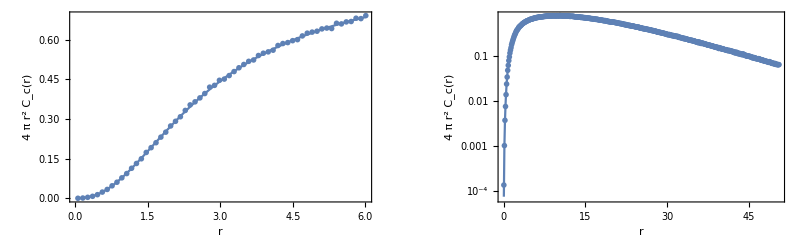

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],1/mfp,c,b]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (1)\nInfinite 3D, isotropic point source, linearly-anisotropic scattering, Gamma-4 random flight - correlated emission\nCollision-rate density C_c[r], c = "<>ToString[c]<>", b = "<>ToString[b]]
```

### Collision-rate density - Exact solution (2) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

((-0.0101764-0.0204849 ⅈ) ⅇ^((-1.33922-0.497388 ⅈ) r)-(0.0101764-0.0204849 ⅈ) ⅇ^((-1.33922+0.497388 ⅈ) r)+0.00360865 ⅇ^(-0.947286 r)+0.0167441 ⅇ^(-0.102038 r))/r

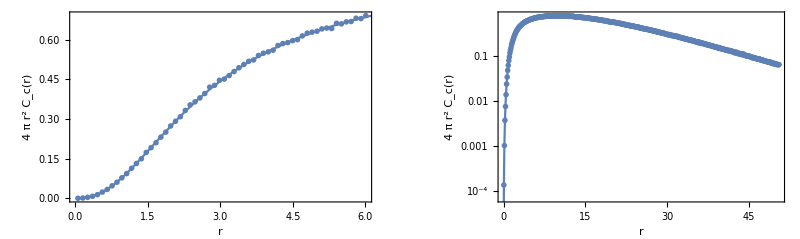

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
CCexactfr=FullSimplify[Chop[Integrate[-(u (-3+b c-2 u^2+u^4) Sin[r u])/(2 π^2 r (b c^2+3 (1+u^2)^4+c (1+u^2) (-3+u^2+b (-1+3 u^2)))),{u,0,Infinity},Assumptions->r>0]]]

plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[4 Pi r^2 CCexactfr,{r,0,maxr},PlotRange->All],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
LogPlot[4 Pi r^2 CCexactfr,{r,0,maxr},PlotRange->All],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (2)\nInfinite 3D, isotropic point source, linearly-anisotropic scattering, Gamma-4 random flight - correlated emission\nCollision-rate density C_c[r], c = "<>ToString[c]<>", b = "<>ToString[b]]
```

## Namespace

```mathematica
End[]
```

inf3DisopointlinanisoscatterGamma4`